# Accelerometer Frequency Response

Guralp CMG-3VL at Humboldt-University

## Definition

```mathematica
cmg3tf::usage="cmg3tf[s] returns the frequency response of the Guralp CMG3 acceleration output.";

(*CMG3 Acceleration Output,fitted by Guralp after calibration measurements made at HUB in 10/2014*)cmg3lowerpolefreq=0.0026;(*Hz*)cmg3poles=2π{-cmg3lowerpolefreq-cmg3lowerpolefreq I,-cmg3lowerpolefreq+cmg3lowerpolefreq I,-42+85*I,-42-85*I,-88.2};
cmg3zeros={0,0};
cmg3tftemp[s_]:=Product[s-nullstelle,{nullstelle,cmg3zeros}]/Product[s-pole,{pole,cmg3poles}];
cmg3gainconst=1/FindMaximum[Abs[cmg3tftemp[I 2π f]],{f,1}][[1]];
cmg3tf[s_]:=cmg3gainconst*cmg3tftemp[s];
(*cmg3tf=cmg3gainconst s^2/((cmg3lowerpolefreq+I cmg3lowerpolefreq+s)(cmg3lowerpolefreq-I cmg3lowerpolefreq+s)(2π 80+s)(2π 120+s)(2π 180+s));*)
cmg3sens=1997 (*V/m/s.b2*);
```

```mathematica
cmg3tf[s]
```

(1.96661×10^8 s^2)/(((0.0163363-0.0163363 ⅈ)+s) ((0.0163363+0.0163363 ⅈ)+s) (554.177+s) ((84-170 ⅈ) π+s) ((84+170 ⅈ) π+s))

## Bode Plot

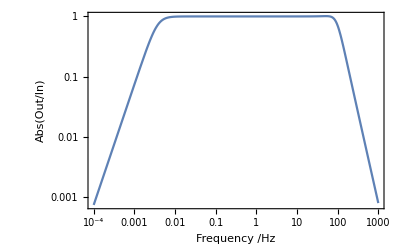

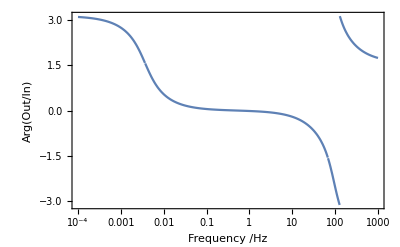

```mathematica
plotOpts={Frame->True,GridLines->Automatic};
fmin=0.0001;fmax=1000;
LogLogPlot[Abs@cmg3tf[ⅈ 2π f],{f,fmin,fmax},Evaluate@plotOpts,FrameLabel->{"Frequency /Hz","Abs(Out/In)"}]
LogLinearPlot[Arg@cmg3tf[ⅈ 2π f],{f,fmin,fmax},Evaluate@plotOpts,FrameLabel->{"Frequency /Hz","Arg(Out/In)"}]
```